## Complete the following problems using Mathematica’s analytical engine

## Series

Evaluate the series below using appropriate Mathematica functions (it should have exact answers):

√12∑_(n=0)^∞ (-3)^-n/(2n+1)

```mathematica
sqrt[12]*Sum[(-3)^-n/(2n+1),{n,0,Infinity}]
```

(π sqrt[12])/(2 √3)

## Differentials

Find the derivatives of the following function f(x), then use Solve to find the extrema of f(x).

f(x) = x^3/(Exp[x]-1)

```mathematica
f[x_] := x^3/(Exp[x]-1)
```

```mathematica
a =f'[x]
```

(3 x^2)/(-1+ⅇ^x)-(ⅇ^x x^3)/((-1+ⅇ^x)^2)

```mathematica
Solve[a==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→3+ProductLog[-3/ⅇ^3]}}

## Integral

Evaluate the integrals below using appropriate Mathematica functions (they should have exact answers):

∫_0^∞ x^n/(Exp[x]-1)ⅆx
∫x^2 sin[x] cos[x]ⅆx

```mathematica
Integrate[x^n/(Exp[x]-1),{x,0,Infinity}]
```

ConditionalExpression[Gamma[1+n] PolyLog[1+n,1], Re[n]>0]

```mathematica
Integrate[x^2 Sin[x]Cos[x],x]
```

-1/8 (-1+2 x^2) Cos[2 x]+1/4 x Sin[2 x]

## Differential Equation

Solve the differential equations and graph the solution

x^2(ⅆ^2 y(x))/(ⅆ x^2) + x(ⅆy(x))/ⅆx+(x^2-4)y(x)=0, where (ⅆy(0))/(ⅆ x)=0

```mathematica
DSolve[x^2*y''[x]+x*y'[x]+(x^2-4)*y[x]==0,y[x],x]
```

{{y[x]→BesselJ[2,x] C[1]+BesselY[2,x] C[2]}}

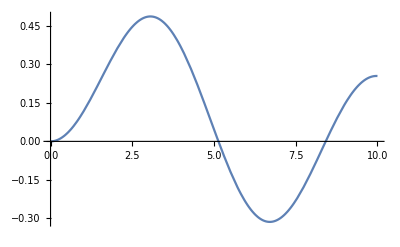

```mathematica
Plot[{BesselJ[2,x]},{x,0,10}]
```